```mathematica
CellVolume = Function[{n,L,A},{L A / n}];
dX = Function[{n,L},L / n];
(*
Index "j" is expected to range from 0≤j<n -- 0 based index
*)
X =Module[{dx,x},Function[{x0,n,L,j},dx = L/n; x=x0 + dx/2 + j dx]];
Y = Module[{x,y},Function[{x0,n,L,j,u},x=X[x0,n,L,j]; y=x+u[x]]];
Horizon=Module[{dx,dCx,nCx},Function[{x0,n,L,r},dx=dX[n,L];dCx=r/dx; nCx=IntegerPart[dCx]; nCx += If[Abs[dCx-nCx]≥ .5,1,0] ]];
(*
Index "i" is expected to range from 0≤i<n -- 0 based index
*)
StartCell = Module[{h},Function[{x0,n,L,r,i},h=Horizon[x0,n,L,r]; If[i>h,i-h,0]]];
(*
Index "i" is expected to range from 0≤i<n -- 0 based index
*)
LastCell = Module[{h},Function[{x0,n,L,r,i},h=Horizon[x0,n,L,r];If[i<(n-h),i+h,n-1]]];
(*
Index "i" is expected to range from 0≤i<n -- 0 based index
*)
WeightedVolumeCell=Module[{cellVolume,dx,xI,start,end,cells,m},
Function[
{x0,n,L,A,r,i},
cellVolume=CellVolume[n,L,A];
dx = dX[n,L];
xI = X[x0,n,L,i];
(*
Select all cells from start to end of neighborhood but delete "this" cell "i"
*)
start=StartCell[x0,n,L,r,i];
end=LastCell[x0,n,L,r,i];
cells=Select[Range[start,end],#≠i&];
(*
This computes a table of zeta squared values, then sums them and multiplies by the cell volume which is assume to be constant
*)
m=cellVolume *Total[Table[Power[X[x0,n,L,j]-xI,2],{j,cells}]]
]
];

WeightedVolume=Function[{x0,n,L,A,r},Table[WeightedVolumeCell[x0,n,L,A,r,i],{i,0,n-1}]];
Dilatation = Module[{start,end,cells,cellVolume,xI,yI,dx,m,d},
Function[{x0,n,L,A,r,i,u},
start=StartCell[x0,n,L,r,i];
end=LastCell[x0,n,L,r,i];
cells=Select[Range[start,end],#≠i&];
cellVolume=CellVolume[n,L,A];
xI = X[x0,n,L,i];
yI = Y[x0,n,L,i,u];
dx = dX[n,L];
m = WeightedVolumeCell[x0,n,L,A,r,i];
d=-3+3*cellVolume*Total[Table[Sqrt[Power[Y[x0,n,L,j,u]-yI,2]*Power[ X[x0,n,L,j]-xI,2]],{j,cells}]]/m
]
];
InternalForce = Module[{f,i,cellVolume,m,θ,ω,α,c,xI,yI,start,end,cells,numNeigh,j,nJ,ξ,dy,dY,t},
Function[{x0,n,L,A,r,u,K,μ},
f=Table[0,{j,0,n-1}];
For[i=0,i<n,i++,
cellVolume=CellVolume[n,L,A];
m = WeightedVolumeCell[x0,n,L,A,r,i];
θ = Dilatation[x0,n,L,A,r,i,u];
ω = 1;
α=15 μ/m;
c = ω * θ*(9 * K - 15 μ)/3/m;
xI = X[x0,n,L,i];
yI = Y[x0,n,L,i,u];
start=StartCell[x0,n,L,r,i];
end=LastCell[x0,n,L,r,i];
cells=Select[Range[start,end],#≠i&];
numNeigh = Length[cells];
For[j=1,j≤ numNeigh,j++,
nJ= cells[[j]];
ξ = Abs[X[x0,n,L,nJ]-xI];
dy = Y[x0,n,L,nJ,u]-yI;
dY = Abs[dy ];
t = (c * ξ + ω * α * (dY-ξ))*cellVolume;
f[[i+1]]+= t*dy/dY;
f[[nJ+1]]-=t*dy/dY;
];
];
f
]
];

(*
Computes y(x[i])-y(x[j])
*)
DeformationState = Module[{yI,yJ},
Function[{x0,n,L,u,i,j},
yI = Y[x0,n,L,i,u];
yJ = Y[x0,n,L,j,u];
yJ-yI
]
];

DirY = Module[{dy,M},
Function[{x0,n,L,u,i,j},
dy=DeformationState[x0,n,L,u,i,j];
M=dy/Abs[dy]
]
];

Bond = Module[{xI,xJ,ξ},
Function[{x0,n,L,i,j},
xI = X[x0,n,L,i];
xJ = X[x0,n,L,j];
ξ=xJ-xI
]
];

(* Compute influence function for bond between points i and j *)
InfluenceFunction =Module[{ω}, 
Function[{x0,n,L,i,j},
ω=1
]
];

ScalarForceState = Function[{x0,n,L,A,r,u,K,μ, i},
0
];

(* Change in force at point i due to changes in displacements at point q *)
(* Note that point q is in the neighborhood of point p *)
TangentStiffness = Module[{c,ζ,ξ,Yξ,dirYζ,dirYξ,ωζ,ωξ,mI,v,tI,kI},
Function[{x0,n,L,A,r,u,K,μ, i,p, q},
c = 9*K-15*μ;
ζ=Bond[x0,n,L,i,p];
ξ=Bond[x0,n,L,i,q];
Yξ = DeformationState[x0,n,L,u,i,q];
dirYζ = DirY[x0,n,L,u,i,p];
dirYξ = DirY[x0,n,L,u,i,q];
ωζ = InfluenceFunction[x0,n,L,i,p];
ωξ = InfluenceFunction[x0,n,L,i,q];
mI = WeightedVolumeCell[x0,n,L,A,r,i];
v = CellVolume[n,L,A];
(* Tangent stiffness contribution at i *)
tI = ScalarForceState[x0,n,L,A,r,u,K,μ, i];
kI = (c * ωζ  * ωξ * Abs[ζ] * Abs[ξ] * dirYζ * dirYξ)*Power[v,2]/Power[mI,2];
kI+=If[p==q,(15* μ/mI)* ωζ  * Power[dirYξ,2] * v,0];
kI+= tI * (1-Power[dirYξ,2])*Power[v,2]/Abs[Yξ]
]
];

StiffnessOperator = Module[{op,i,startI,endI,cellsI,numNeighI,j,p,startJ,endJ,cellsJ,numNeighJ,k,q,opIQ,sumI},
Function[{x0,n,L,A,r,u,K,μ},
(* Stiffness Matrix *)
op=Table[0,{i,0,n-1},{j,0,n-1}];

(* Loop over all points "i" in messh *)
For[i=0,i<n,i++,
(*
Get neighborhood of point i 
-- these neighbors are denoted as p
*)
startI=StartCell[x0,n,L,r,i];
endI=LastCell[x0,n,L,r,i];
cellsI=Range[startI,endI];
numNeighI = Length[cellsI];
(* Loop over neighbors p of ith cell *)
For[j=1,j≤ numNeighI,j++,
p=cellsI[[j]];
startJ=StartCell[x0,n,L,r,p];
endJ=LastCell[x0,n,L,r,p];
cellsJ=Range[startJ,endJ];
numNeighJ = Length[cellsJ];
(* Loop over neighbors q of the pth cell
    --assemble stiffness 
  Stiffness contribution is for equation "i" due to displacments at point "q" 
*)
For[k=1,k≤ numNeighJ,k++,
q=cellsJ[[k]];
If[q==i,Continue[]];
opIQ=0;
opIQ += If[(i==q) || (i==p), 0, TangentStiffness [x0,n,L,A,r,u,K,μ,i,p, q]];
opIQ -= If[(p==i) || (p==q), 0, TangentStiffness [x0,n,L,A,r,u,K,μ, p, i, q]];
opIQ += If[(q==i) || (q==p), 0, TangentStiffness [x0,n,L,A,r,u,K,μ, q, i, p]];
(*op[[i+1,q+1]]+=If[q==i,0, opIQ];*)
op[[i+1,q+1]]+=opIQ;
];
];
];

(* Loop over all points "i" in mesh and assemble diagonal (row sum) *)
For[i=0,i<n,i++,
sumI = Total[op[[i+1]]];
op[[i+1,i+1]]-=sumI;
];
op
]
];

ZeroDisplacement := Function[{},
0&
];

LinearDisplacement := Function[{x0},
#-x0&
];

DisplacementProbe := Function[{x0,n,L,i,δ},
If[
x0+i*dX[n,L] < #  && # < x0 + (i+1)*dX[n,L],
δ,
0
] &
];
```

```mathematica
x0=0;n=11;L=1;A=1;r=.1;
u=ZeroDisplacement[];
Clear[K,ν];e=3*K*(1-2.0*ν);μ=e/(2*(1+ν));
MatrixForm[FullSimplify[StiffnessOperator[x0,n,L,A,r,u,K,μ]]/.{ν->1/4,K->130000.0}]
```

({-2.12355×10^8} | {2.12355×10^8} | {0.} | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
{2.12355×10^8} | {-3.53925×10^8} | {1.4157×10^8} | {0.} | 0 | 0 | 0 | 0 | 0 | 0 | 0
{0.} | {1.4157×10^8} | {-2.8314×10^8} | {1.4157×10^8} | {0.} | 0 | 0 | 0 | 0 | 0 | 0
0 | {0.} | {1.4157×10^8} | {-2.8314×10^8} | {1.4157×10^8} | {0.} | 0 | 0 | 0 | 0 | 0
0 | 0 | {0.} | {1.4157×10^8} | {-2.8314×10^8} | {1.4157×10^8} | {0.} | 0 | 0 | 0 | 0
0 | 0 | 0 | {0.} | {1.4157×10^8} | {-2.8314×10^8} | {1.4157×10^8} | {0.} | 0 | 0 | 0
0 | 0 | 0 | 0 | {0.} | {1.4157×10^8} | {-2.8314×10^8} | {1.4157×10^8} | {0.} | 0 | 0
0 | 0 | 0 | 0 | 0 | {0.} | {1.4157×10^8} | {-2.8314×10^8} | {1.4157×10^8} | {0.} | 0
0 | 0 | 0 | 0 | 0 | 0 | {0.} | {1.4157×10^8} | {-2.8314×10^8} | {1.4157×10^8} | {0.}
0 | 0 | 0 | 0 | 0 | 0 | 0 | {0.} | {1.4157×10^8} | {-3.53925×10^8} | {2.12355×10^8}
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | {0.} | {2.12355×10^8} | {-2.12355×10^8})

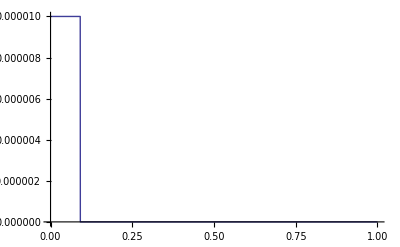

{{-2.12355×10^8},{2.12355×10^8},{0.},{0},{0},{0},{0},{0},{0},{0},{0}}

```mathematica
u=DisplacementProbe[x0,n,L,0,δ]/.δ->.00001;
Plot[u[x],{x,x0,x0+L}]
FullSimplify[(InternalForce[x0,n,L,A,r,u,K,μ]/δ) /.{δ->.00001,ν->1/4, K->130000.0}]
```